```mathematica
Clear["Global`*"]
```

```mathematica
a=2.46;(*a is given in units of 10^-10*)
b=(4π)/(√3*a); (*Magnitude of reciprocal vectors*)
b1=b*{(√3)/2.,1/2.}; (*Reciprocal vectors b1,b2*)
b2=b*{(-√3)/2.,1/2.};
b3=(b1+b2);
kk=1/3.(2  b1+b2) ;
kp=1/3.(b1-b2) ;

n=2100;(*Nk=3 n^2*) (* n = number of points that the mesh of the full 1BZ (with same Δk distance) would have*)
δn=60; (* δn = parameter analogous to n, but for the mini-kmesh*)
λ=(n-δn); (* λ is used when generating the meshes*)
Nq=80; (*Nq = is the number of q points for which Π(q) will be calculated*)
{iqf,jqf}={0,Nq}; (*The indices of the vector pointing to the end of the q-path*)
(*In order to move in other direction, it might be convenient to project j along other kp vector*)
{i0,j0}={0,n}; (*Center of k mesh*)

(*This function transltes from indices i,j to vectors: *)
IndexToVector[kij_]:=Module[{sol},
sol=Table[kij[[i,j]].(1/n{kk,kp}),{i,1,Length[kij]},{j,1,Length[kij[[i]]]}]
];

(*kij the indices of the vectors in the k-mesh: *)
(*
kij=Module[{sol},
sol=Table[{i,j},{i,-n+1,n},{j,Max[-n,-n-i]+1,Min[n,n-i]}]
];
kmesh=IndexToVector[kij];
*)
(*Shifted mesh, scaled, including all the q path*)

kqpathij=Module[{sol},
sol=Table[{i+i0,j+j0},{i,-(n-λ)+1,(n-λ)},{j,Max[-(n-λ),-(n-λ)-i]+1,Min[(n-λ),(n-λ)-i]+jqf}]
];
kqpathmesh=IndexToVector[kqpathij];

k0ij=Module[{sol},
sol=Table[{i+i0,j+j0},{i,-(n-λ)+1,(n-λ)},{j,Max[-(n-λ),-(n-λ)-i]+1,Min[(n-λ),(n-λ)-i]}]
];
k0mesh=IndexToVector[k0ij];

kfij=Module[{sol},
sol=Table[{i+i0,j+j0+jqf},{i,-(n-λ)+1,(n-λ)},{j,Max[-(n-λ),-(n-λ)-i]+1,Min[(n-λ),(n-λ)-i]}]
];
kfmesh=IndexToVector[kfij];


StringForm["Total number of k-points to be diagonalized: ``.",Length[Flatten[kqpathij,1]]]
```

Total number of k-points to be diagonalized: 20400.

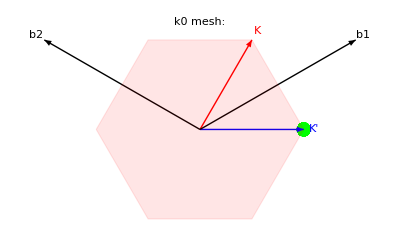

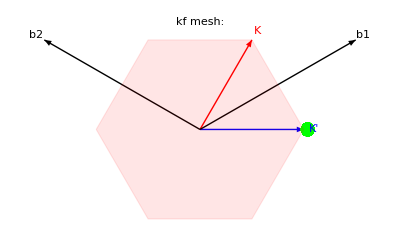

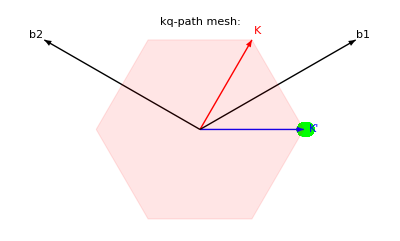

```mathematica
(*Drawing the contours and vectors of the 1BZ for the figures: *)
BZcontour = Polygon[{((4π)/(3a))*{-1,0},((4π)/(3a))*{(-1)/2,(√3)/2},((4π)/(3a))*{1/2,(√3)/2},((4π)/(3a))*{1,0},((4π)/(3a))*{1/2,(-√3)/2},((4π)/(3a))*{(-1)/2,(-√3)/2}}];
ps=0.015;
BZvectors =Graphics[{
Red,Arrow[{{0,0},kk}],
Blue,Arrow[{{0,0},kp}],
Black,Arrow[{{0,0},b1}],
Black,Arrow[{{0,0},b2}],
Black, Text["b1",b1*1.05],
Black, Text["b2",b2*1.05],
Red, Text["K",kk*1.1],
Blue, Text["K'",kp*1.1],
Red,Opacity[0.1],EdgeForm [Dashed],BZcontour
}];

(*Plotting the k mesh: *)

Show[
Graphics[{
Text["k0 mesh:",0.6b3],
PointSize[ps],
Green,
Point[Flatten[k0mesh,1]]
}],Graphics[{
PointSize[ps],
Green,
Opacity[.0],
Point[Flatten[kfmesh,1]]
}],
BZvectors
]
Show[
Graphics[{
Text["kf mesh:",0.6b3],
PointSize[ps],
Green,
Point[Flatten[kfmesh,1]]
}],
BZvectors
]

Show[
Graphics[{
Text["kq-path mesh:",0.6b3],
PointSize[ps],
Green,
Point[Flatten[kqpathmesh,1]]
}],
BZvectors
]
```

```mathematica
a=2.46;(*a is given in units of 10^-10*)
γ0=3.1;
γ1=0.38;
γ2=-0.015;
γ3=0.29;
γ4=0.141;
δ=-0.0105;
Δ1=0.05;
Δ2=-0.0023;
u[kx_,ky_]=1.+2.*Cos[0.5*kx*a]*Exp[-ⅈ*ky*a*0.5*√3];
v[kx_,ky_]=Exp[ⅈ*ky*a*√3]*u[kx,ky];
Hk[kx_,ky_]={{Δ1+Δ2,-γ0*u[kx,ky],γ4*u[kx,ky]*,γ1,0,0},{-γ0*u[kx,ky]*,Δ1+Δ2+δ,γ3*v[kx,ky],γ4*u[kx,ky]*,0.5*γ2,0},{γ4*u[kx,ky],γ3*v[kx,ky]*,-2.*Δ2,-γ0*u[kx,ky],γ4*v[kx,ky]*,γ1},{γ1,γ4*u[kx,ky],-γ0*u[kx,ky]*,-2.*Δ2,γ3*u[kx,ky],γ4*u[kx,ky]*},{0,0.5*γ2,γ4*v[kx,ky],γ3*u[kx,ky]*,Δ2-Δ1+δ,-γ0*v[kx,ky]},{0,0,γ1,γ4*u[kx,ky],-γ0*v[kx,ky]*,Δ2-Δ1}};
(*Number of bands*)
Nb=Length[Hk[kx,ky]];
```

```mathematica
μ=-0.052175;(* VHS is at μ=-0.052175;*)
kbT=0.0000861*1; (*Boltzmann's k × temperature*)
δc=10.*kbT; (*cutoff for the Fermi-Dirac distribution*)
FDif[ϵk_]=If[Abs[μ-ϵk]<δc,1/(1+Exp[(ϵk-μ)/kbT]),UnitStep[μ-ϵk]];
δFif[ϵk_]=If[Abs[μ-ϵk]<δc,-1./kbT/(2*(1+Cosh[(ϵk-μ)/kbT])),0.];
```

```mathematica
(*These arrays hold the same {i,j} structure than kij*)
Ekqpathij=Map[Eigenvalues,Apply[Hk,kqpathmesh,{2}],{2}];
ψkqpathij=Map[Eigenvectors,Apply[Hk,kqpathmesh,{2}],{2}];
nfEkqpathij=Map[UnitStep[μ-#]&,Ekqpathij,{2}];

Ek=Flatten[Apply[Ekqpathij[[#1+(n-λ),#2-j0-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1];
ψk=Flatten[Apply[ψkqpathij[[#1+(n-λ),#2-j0-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1];
nfEk=Flatten[Apply[nfEkqpathij[[#1+(n-λ),#2-j0-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1];
```

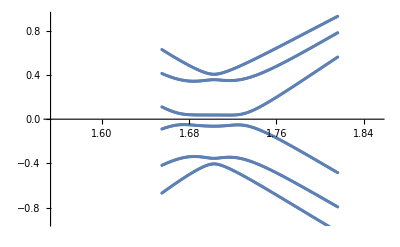

```mathematica
i=0;
Epath=Flatten[Table[{kqpathmesh[[i+(n-λ),ii]][[1]],Ekqpathij[[i+(n-λ),ii]][[j]]},{ii,Length[kqpathmesh[[i+(n-λ)]]]},{j,Nb}],1];
K0=Norm[kp];
δK=0.15;
δE=0.3γ0;
ListPlot[Epath,PlotRange->{{K0-δK,K0+δK},{-δE,δE}}]
```

```mathematica
qstep=1.;(*size of q-steps in units of Δk spacings*)
Δqij={0.,qstep};
Δq=Norm[Δqij.{kk/n,kp/n}];
Lq=Δq*Nq;
qi=Table[{0. (-Lq/2)+i Δq,0.},{i,0,Nq}];
ω=0.;
Πq0=Table[0,{i,0,Nq}];
kpij=kij;
```

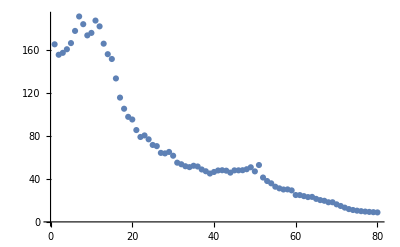

```mathematica
Monitor[
For[i=0,i≤Nq/qstep,i++,
q=i Δq;  (*Used for progress bar only*)
Ekq=Flatten[Apply[Ekqpathij[[#1+(n-λ),#2+i qstep-j0-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1];
ψkq=Flatten[Apply[ψkqpathij[[#1+(n-λ),#2+i qstep-j0-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1];
nfEkq=Flatten[Apply[nfEkqpathij[[#1+(n-λ),#2+i qstep-j0-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1];

Δnf=Flatten[Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Length[nfEk]}]];
ΔE=Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]]-Tuples[{Ek[[i]],Ekq[[i]]}][[All,2]],{i,Length[Ek]}]]+ω;(*+ⅈ*η*)
ψTuples=Table[Tuples[{ψk[[i]],ψkq[[i]]*}],{i,Length[Ek]}];
Fkq=Flatten[Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Length[Ek]},{j,Nb^2}]];
idiv=Flatten[Position[Abs[ΔE],_?(#==0.&)]];
ΔE[[idiv]]=1.;

Δnf[[idiv]]=Map[δFif[#]&,Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]],{i,Length[Ek]}]][[idiv]]];

Πq0[[i+1]]=-(2/Length[Ek])*Total[Δnf*Re[1/ΔE]*Fkq]
]
,Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[q,{0.,Lq*1.05/qstep}],StringForm["``%",NumberForm[100*q/(Lq*1.05/qstep),{3,2}]]},{Text[Style["Current value of q: ",Darker[Blue,0.66]]],q ,StringForm["Final value: ``",NumberForm[Lq]] }},Alignment->Left,Dividers->Center]];
ListPlot[Table[{i,Re[Πq0[[i]]]},{i,1,Nq}]]
```

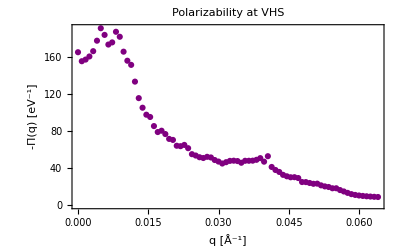

```mathematica
Show[ListPlot[Table[{qi[[i,1]],Re[Πq0[[i]]]},{i,1, Nq}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True, FrameLabel->{"q [Å^-1]",-"Π(q) [eV^-1]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Polarizability at VHS"]]]
```